```mathematica
Print["Final Project"]
MyFolder=NotebookDirectory[]

DataParks=Import[StringJoin[MyFolder,"MergedNPSData_WikiNP_2017FTEBudget_FINAL.csv"],"csv"];
Length[DataParks]
```

Final Project

/Users/soloriojuarez/Downloads/

62

```mathematica
filteredDataParks=Select[DataParks,#[[3]]=="California"&];
filteredDataParks
```

{{Channel Islands,Channel Islands NP,California,34.01,-119.42,1980,1009.9,383687,58.,62.,7577.},{Death Valley,Death Valley NP,California,36.24,-116.82,1994,13650.3,1294827,70.,99.,8912.},{Joshua Tree,Joshua Tree NP,California,33.79,-115.9,1994,3199.6,2853619,46.,107.,6283.},{Kings Canyon,Sequoia NP & Kings Canyon NP,California,36.8,-118.55,1940,1869.2,692932,163.,310.,17150.},{Lassen Volcanic,Lassen Volcanic NP,California,40.49,-121.51,1916,431.4,507256,47.,72.,5397.},{Pinnacles,Pinnacles NP,California,36.48,-121.16,2013,108.,233334,32.,43.,3603.},{Redwood,Redwood NP,California,41.3,-124.,1968,562.5,445000,89.,118.,9096.},{Sequoia,Sequoia NP & Kings Canyon NP,California,36.43,-118.68,1890,1635.2,1291256,163.,310.,17150.},{Yosemite,Yosemite NP,California,37.83,-119.5,1890,3082.7,4336890,250.,634.,31064.}}

```mathematica
FDPsort= filteredDataParks[[All,{7,8}]]
```

{{1009.9,383687},{13650.3,1294827},{3199.6,2853619},{1869.2,692932},{431.4,507256},{108.,233334},{562.5,445000},{1635.2,1291256},{3082.7,4336890}}

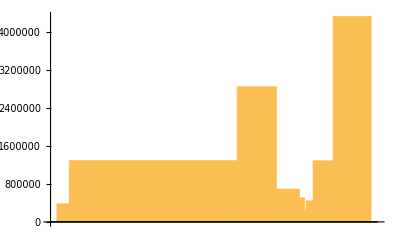

```mathematica
RectangleChart[FDPsort]
```

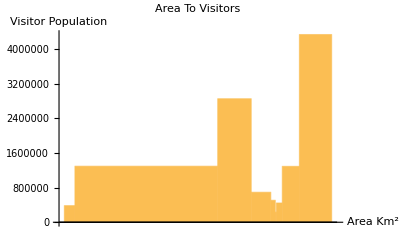

```mathematica
Show[%87,AxesLabel->{HoldForm[Area Km^2],HoldForm[Visitor Population]},PlotLabel->HoldForm[Area To Visitors],LabelStyle->{8,GrayLevel[0],Bold,Italic}]
```

```mathematica
FDPsort2= filteredDataParks[[All,{7,11}]]
```

```mathematica
{{1009.9,7577.},{13650.3,8912.},{3199.6,6283.},{1869.2,17150.},{4
.4,5397.},{108.,3603.},{562.5,9096.},{1635.2,17150.},{3082.7,31064.}}
```

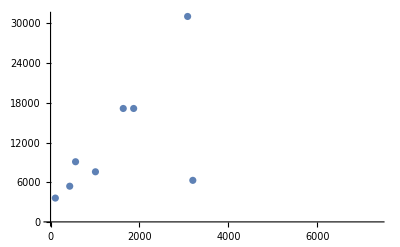

```mathematica
ListPlot[FDPsort2]
```

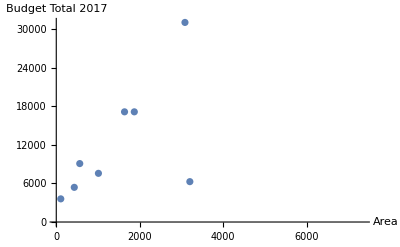

```mathematica
Show[%93,AxesLabel->{HoldForm[Area],HoldForm[Budget Total 2017]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

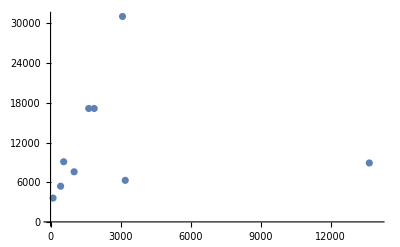

```mathematica
ListPlot[FDPsort2,PlotRange->{{0,14000},All}]
```

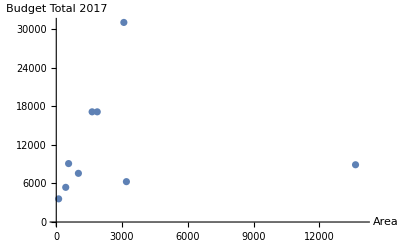

```mathematica
Show[%95,AxesLabel->{HoldForm[Area],HoldForm[Budget Total 2017]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

```mathematica
Show[%96,AxesStyle->Black]
```

-Graphics-

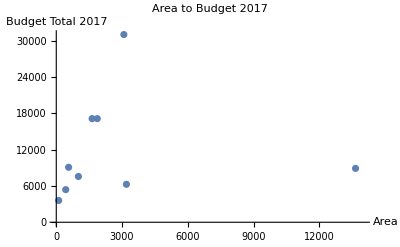

```mathematica
Show[%97,PlotLabel->HoldForm[Area to Budget 2017]]
```